```mathematica
dim=8;
Clear[μ,η, A]
(* Parameters to eliminate the magnetic field *)
η=1;
A[1]=1;
A[2]=1;
A[5]=1;
A[6]=B[6]=μ;
A[7]=B[7]=η; (*A[3]=κ; A[4]=λ*)
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/4)*A[4]^(-(x0*x2+x2*x4)/4)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]/2]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/4)*B[4]^(-(x0*x4)/4)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0≤1,x0+=2,For[x2=-1,x2≤1,x2+=2,For[x4=-1,x4≤1,x4+=2,leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];]]]
(*Equates the unrenormalized with the renormalized variables*)

req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4]==leq[4];
req[5]==leq[5];
req[6]==leq[6];
req[7]==leq[7];
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0][[1]];
SB[0]={B[0]->2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0&&B[2]>0&&B[4]>0&&B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0&&B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>=0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0&&B[5]>0&&B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>=0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}]
```

{B[0]→2 (A[0]+Log[(μ √(A[3]/(μ+A[3]+μ^2 A[3]+μ A[3]^2)))/(1+μ)]),B[1]→1,B[2]→1,B[3]→((1+μ)^2 A[3] A[4])/(1+μ A[3])^2,B[4]→(μ+A[3])^2/(1+μ A[3])^2,B[5]→1}

Recursive Equation Flow

```mathematica
SIC={B[0]->1,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
Sκλ={A[0]->C,A[1]->1,A[2]->1,A[3]->κ,A[4]->λ,A[5]->1}; (*Just for comparison; not being used in RG flow*)
Sκλ2={κ->A[3],λ->A[4],μ->μ}; (*Just for comparison; not being used in RG flow*)
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
kap[μ_,κ_,λ_]:=(κ λ (1+μ)^2)/(1+κ μ)^2
lam[μ_,κ_,λ_]:=(κ+μ)^2/(1+κ μ)^2
Factor[SBT/.Sκλ]
```

{B[0]→2 (C+Log[(μ √(κ/(κ+μ+κ^2 μ+κ μ^2)))/(1+μ)]),B[1]→1,B[2]→1,B[3]→(κ λ (1+μ)^2)/(1+κ μ)^2,B[4]→(κ+μ)^2/(1+κ μ)^2,B[5]→1}

Jacobian Setup

```mathematica
Clear[μ,κ,λ]
Jaco = Factor[{{D[kap[μ,κ,λ],κ], D[kap[μ,κ,λ],λ]},{D[lam[μ,κ,λ],κ],D[lam[μ,κ,λ],λ]}}];
Jaco//MatrixForm
Jc = Factor[Eigenvalues[Jaco]]
```

(-(λ (1+μ)^2 (-1+κ μ))/(1+κ μ)^3 | (κ (1+μ)^2)/(1+κ μ)^2
-(2 (-1+μ) (1+μ) (κ+μ))/(1+κ μ)^3 | 0)

{-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4))),-1/(2 (1+κ μ)^3)(1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2-√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4)))}

RG flow and convergence check:

* General Parameters

```mathematica
nprec=2000;
μV=N[{1.0,2.0,3.0,4.0,5.0,10,20,100},nprec];
TV=N[2/Log[μV],8]
kmaxV={100,3000,100000,100000,100000,10000,10000,10000};
ind=0;
```

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,2.88539,1.82048,1.4427,1.24267,0.86858896,0.6676164,0.43429448}

```mathematica
Clear[λκ,Jocnum,λκ1,Jocnum1,λκ2,Jocnum2,λκ3,Jocnum3,λκ4,Jocnum4,λκ5,Jocnum5,λκ6,Jocnum6,λκ7,Jocnum7]
```

1) μ=1.0; kmax=3000

```mathematica
ind=1; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
lki=ConstantArray[0,{kmax,2}];
Part[lki,1][[1]]=lam[μ,μ,1]
Part[lki,1][[2]]=kap[μ,μ,1]
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
If[i>1,
Part[lki,i][[1]]=lam[μ,Part[lki,i-1][[2]],Part[lki,i-1][[1]]];
Part[lki,i][[2]]=kap[μ,Part[lki,i-1][[2]],Part[lki,i-1][[1]]],
];
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ1=λκ;(* change here *)
Jocnum1=Jocnum; (* change here*)
```

1.

1.

```mathematica
lki
```

{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}

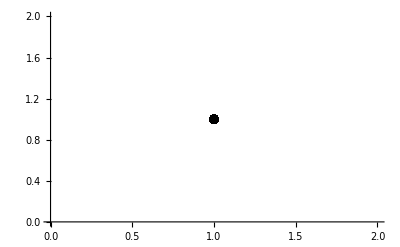

{κ,λ} for the last 50 iterations:(1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.)

```mathematica
λκ=λκ1; (* change here *)
kmax=kmaxV[[1]]; (* change here *)
xyrange={{0.5,1.5},{0,1.5}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black];
Show[Table[Plt[i],{i,1,7}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

2) μ=2.0; kmax=3000

```mathematica
ind=2; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ2=λκ;(* change here *)
Jocnum2=Jocnum; (* change here*)
```

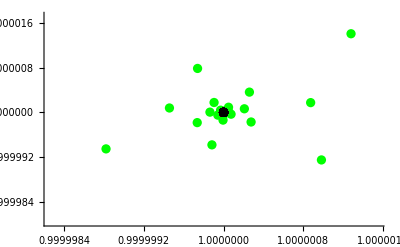

{κ,λ} for the last 50 iterations:(1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.
1. | 1.)

```mathematica
λκ=λκ2; (* change here *)
kmax=kmaxV[[2]]; (* change here *)
xyrange={{0.5,1.5},{0,1.5}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black];
Show[Table[Plt[i],{i,1,7}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

3) μ=3.0; kmax=100000

```mathematica
ind=3; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ3=λκ;(* change here *)
Jocnum3=Jocnum; (* change here*)
```

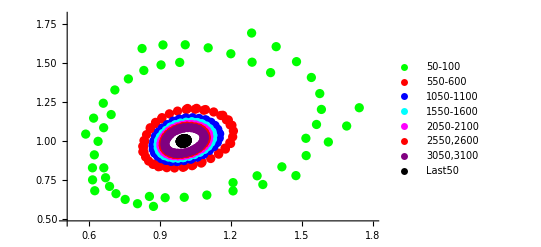

{κ,λ} for the last 50 iterations:(1.01429 | 1.00697
0.999811 | 0.985913
0.986006 | 1.00019
1.00722 | 1.01419
1.01054 | 0.992827
0.987617 | 0.989571)

```mathematica
λκ=λκ3; (* change here *)
kmax=kmaxV[[3]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
(*xyrange=Automatic;*)
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
```

4) μ=4.0; kmax=100000

```mathematica
ind=4; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ4=λκ;(* change here *)
Jocnum4=Jocnum; (* change here*)
```

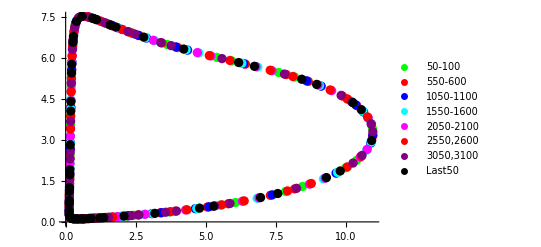

{κ,λ} for the last 50 iterations:(5.27647 | 0.575865
0.155449 | 0.176096
0.260187 | 6.56513
10.2539 | 4.35791
0.632828 | 0.115092
0.146016 | 1.72115)

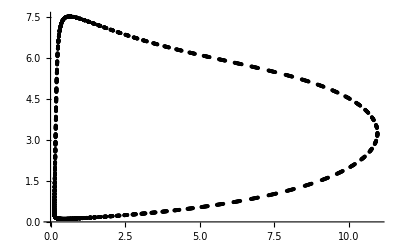

```mathematica
λκ=λκ4; (* change here *)
kmax=kmaxV[[4]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black]
```

5) μ=5.0; kmax=100000

```mathematica
ind=5; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ5=λκ;(* change here *)
Jocnum5=Jocnum; (* change here*)
```

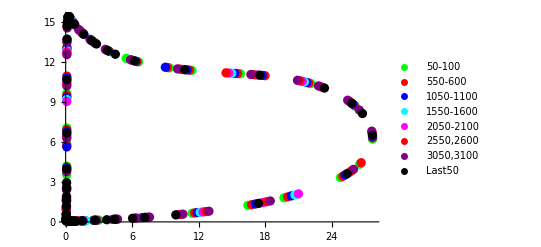

{κ,λ} for the last 50 iterations:(0.431944 | 0.0555029
0.0864467 | 2.95538
4.4837 | 12.6125
3.71212 | 0.163997
0.0572793 | 0.198373
0.247192 | 15.4555)

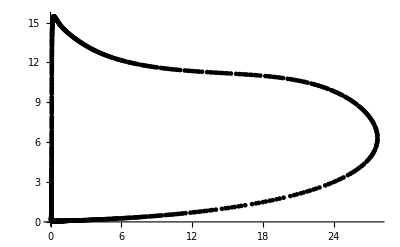

```mathematica
λκ=λκ5; (* change here *)
kmax=kmaxV[[5]]; (* change here *)
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",Table[Part[λκ,i],{i,kmax-5,kmax}]//MatrixForm];
ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-1000,kmax}],PlotRange->Full,PlotStyle->Black]
```

6) μ=10.0; kmax=10000

```mathematica
ind=6; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec*2];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ6=λκ;(* change here *)
Jocnum6=Jocnum; (* change here*)
```

Divide::infy: Infinite expression 1/0.-2.9349956802315367 encountered.

Infinity::indet: Indeterminate expression 0.-3.182826500014224\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.-2.9349956802315367 encountered.

Infinity::indet: Indeterminate expression 0.-3.182826500014224\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.-1.9692101880129635 encountered.

General::stop: Further output of Divide :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.-0.2015446625931475\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

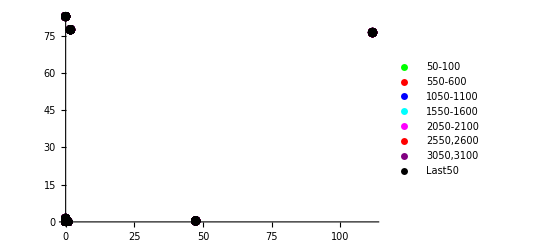

{κ,λ} for the last 50 iterations:(111.7424307 | 76.25427865
0.8242415576 | 0.01184870107
0.01383374087 | 1.371588915
1.771768422 | 77.38534745
47.35292732 | 0.3955297798
0.01006434167 | 0.01460781168)

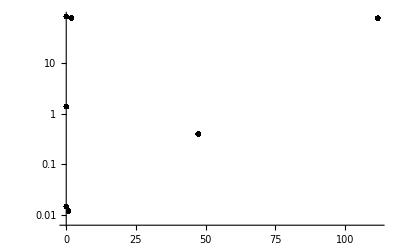

<|82.71427309→143,76.25427865→143,0.01184870107→143,1.371588915→143,77.38534745→143,0.3955297798→143,0.01460781168→143|>

```mathematica
λκ=λκ6; (* change here *)
kmax=kmaxV[[6]]; (* change here *)
kmax=4600;
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
Counts[N[Table[Part[λκ,i][[2]],{i,kmax-1000,kmax}],10]]
```

```mathematica
iind=4890;
N[Table[λκ6[[i]],{i,iind,iind+10}],20]
```

{{0.824,0.012},{0.014,1.4},{1.8,77.4},{50.,0.4},{0.01,0.01},{0.01,80.},{100.,80.},{0.8,0.01},{Indeterminate,ComplexInfinity},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

```mathematica
kap[N[10,1000],N[80,1000],N[100,1000]]
```

1.50872582804577923039396759044951613230029254941934317434043899557513158489466194722265083751428068223085687210587265294162571442376180835129621057323788460429456936631956621015241559785598837907048149862609316381988182686747682749871025762116954306492664444101552210797676437536724537524099868921650683212775541185253763631914538786566729166569254100289743937431518965837023321347691166316760728240760223254016125286587770280906669409804535840810721928425922029423270849016756520017892740192113166905911929688388889668189419904270722770070495526035651440692891688136396296140436190093219929520059974968866943785935495736446794814845986836055430088170062079080300685316886974926784715111104876706862988056440061658258013937010696679088717131051853098732701476462786061742422471286671934738256330647863703454327533778781516861725589579816739687126422807944501333383208567318317770701728956158110726136648789512485173807397432360610410519933728282842451928846744316171577039312594587601951991970087328

7) μ=20.0; kmax=100000

```mathematica
ind=7; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec*2];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ7=λκ;(* change here *)
Jocnum7=Jocnum; (* change here*)
```

Power::infy: Infinite expression 1/0.-4.339680962317018^3 encountered.

Infinity::indet: Indeterminate expression 0.-9.586459379749154\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.-4.339680962317018^3 encountered.

Infinity::indet: Indeterminate expression 0.-9.586459379749154\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.-7.386225886118141 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.-3.038650966653037\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

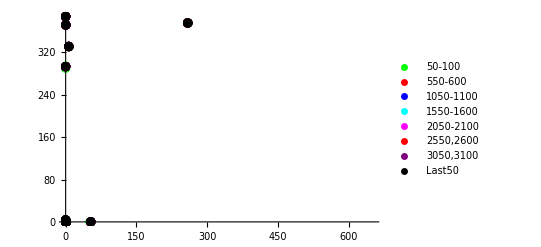

{κ,λ} for the last 50 iterations:(53.20619307 | 0.03860938936
0.0007985341252 | 0.004723842592
0.001611629231 | 387.5540849
258.5121236 | 375.4696622
1.600680128 | 0.002900670553
0.001878692543 | 0.4281037324)

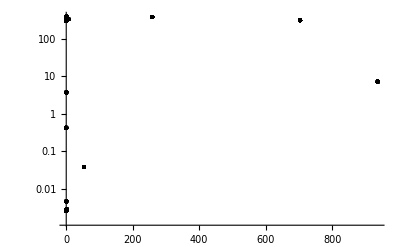

<|331.0405802→72,0.03860938936→72,0.004723842592→72,387.5540849→72,375.4696622→72,0.002900670553→72,0.4281037324→72,371.623819→71,7.175551477→71,0.002607531392→71,293.0734821→71,306.8932404→71,0.002643715697→71,3.724219278→71|>

```mathematica
λκ=λκ7; (* change here *)
kmax=kmaxV[[7]]; (* change here *)
kmax=4600;
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-2000,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
Counts[N[Table[Part[λκ,i][[2]],{i,kmax-1000,kmax}],10]]
```

8) μ=100.0; kmax=100000

```mathematica
ind=8; (* change here *)
Clear[μ,η]
kmax=kmaxV[[ind]];
μ=N[μV[[ind]],nprec*2];
η=N[1.0,nprec];
λκ=ConstantArray[0,{kmax,2}];
Jocnum=ConstantArray[0,{kmax,2}];
InitRG;
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ,i][[1]]=A[3]/.SAT;
Part[λκ,i][[2]]=A[4]/.SAT;
Jciter=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum,i][[2]]=Jciter[[2]];
]
λκ8=λκ;(* change here *)
Jocnum8=Jocnum; (* change here*)
```

Divide::infy: Infinite expression 1/0.-21.764060176803184 encountered.

Infinity::indet: Indeterminate expression 0.-13.86264717612138\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.-21.764060176803184 encountered.

Infinity::indet: Indeterminate expression 0.-13.86264717612138\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.-0.056869661379320015 encountered.

General::stop: Further output of Divide :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.-4.014676020473794\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

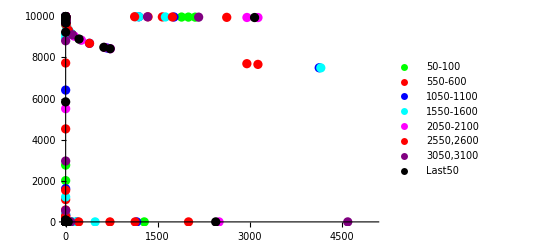

{κ,λ} for the last 50 iterations:(37590.22082 | 15.15212089
0.0004111886005 | 0.0001005327075
0.0003890366929 | 9225.776807
33922.33165 | 9265.157766
0.2786182849 | 0.0001005903918
0.0003432109843 | 12.07171572)

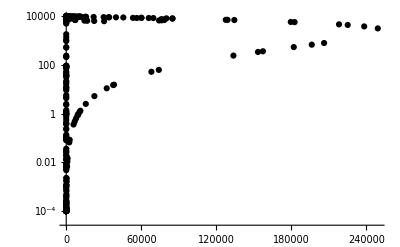

<|1860.057489→1,6396.216802→1,0.0001006591646→1,19.88863625→1,9180.885748→1,0.0004970024385→1,0.0003490950731→1,9991.201048→1,9968.746241→1,0.000112959245→1,0.02764092632→1,9964.142421→1,4414.670845→1,0.0001000882563→1,1121.226579→1,6638.37968→1,0.0001011617498→1,6.228527262→1,9517.893522→1,0.00578386283→1,0.0001336336897→1,9981.617257→1,9974.999203→1,0.0001163374673→1,0.01818573444→1,9970.468153→1,6163.883611→1,0.0001001165649→1,460.0518895→1,7280.176379→1,0.000103431618→1,0.6321573345→1,9837.636005→1,3.577975271→1,0.0001010822142→1,9617.407784→1,9620.497843→1,0.0001010875661→1,3.43698456→1,9636.923338→1,0.02832369267→1,0.0001132840156→1,9962.918612→1,9957.325256→1,0.0001094437346→1,0.04964578322→1,9952.750771→1,2075.771287→1,0.0001000794315→1,2951.309793→1,6366.449738→1,0.0001004123151→1,48.51403395→1,8795.329953→1,0.0001813083797→1,0.001776618737→1,9988.121976→1,9788.219663→1,0.0001018720164→1,1.152009079→1,9784.885357→1,0.6384728497→1,0.0001025754474→1,9835.386807→1,9830.650143→1,0.0001023777779→1,0.7165358371→1,9828.969918→1,2.531437869→1,0.0001012857542→1,9677.075932→1,9677.123935→1,0.000101269113→1,2.515051511→1,9687.079161→1,0.06782671678→1,0.0001082642917→1,9944.189247→1,9938.731638→1,0.0001065483597→1,0.09929250738→1,9934.204691→1,534.4649642→1,0.0001001110838→1,5892.426099→1,7155.653723→1,0.0001002553846→1,94.14505726→1,8424.233847→1,0.0001295149768→1,0.008875198756→1,9977.804861→1,8258.215189→1,0.0001002370487→1,83.11429528→1,8500.25243→1,0.000135468462→1,0.006447611745→1,9980.613011→1,8837.744395→1,0.0001003490394→1,35.8768946→1,8941.229526→1,0.0002343546562→1,0.0009391388484→1,9990.138159→1,9906.210324→1,0.0001042379646→1,0.2300096999→1,9901.338515→1,63.66746205→1,0.0001002701194→1,8453.093274→1,8640.621343→1,0.0001003544175→1,36.3704443→1,8934.926362→1,0.0002312396583→1,0.0009650271684→1,9990.071603→1,9902.998236→1,0.0001040965862→1,0.2457302373→1,9898.131649→1,53.13378599→1,0.0001002936318→1,8581.048367→1,8737.498121→1,0.0001003748588→1,32.05546109→1,8991.368431→1,0.0002633430801→1,0.0007562932423→1,9990.605578→1,9927.931486→1,0.0001055291763→1,0.1373873105→1,9923.076879→1,245.901801→1,0.0001001495357→1,7091.68274→1,7751.363017→1,0.0001002627169→1,77.36490397→1,8542.314976→1,0.0001394616061→1,0.005383420578→1,9982.004603→1,9080.851316→1,0.0001004383273→1,22.16889176→1,9141.963447→1,0.0004219071082→1,0.0004068812326→1,9991.251438→1,9963.794822→1,0.0001111417194→1,0.03649387719→1,9959.150275→1,3230.035623→1,0.0001000802503→1,1855.239272→1,6397.022494→1,0.0001006610042→1,19.77864763→1,9182.904636→1,0.000501390539→1,0.0003464582261→1,9991.195624→1,9968.962689→1,0.0001130523255→1,0.02728196849→1,9964.360648→1,4471.469152→1,0.0001000888198→1,1092.944971→1,6654.103329→1,0.0001011967362→1,5.853607582→1,9531.655385→1,0.006776001646→1,0.0001304825303→1,9980.358596→1,9973.920242→1,0.0001156395472→1,0.01966442213→1,9969.385642→1,5855.629874→1,0.0001001094757→1,549.0480693→1,7143.577823→1,0.0001027473401→1,1.011206538→1,9796.536433→1,0.9188682867→1,0.0001021409222→1,9803.335616→1,9799.18164→1,0.0001020115413→1,0.9990669847→1,9799.169226→1,0.9650884414→1,0.0001020881627→1,9798.580435→1,9794.530376→1,0.0001019669785→1,1.044668929→1,9794.796259→1,0.8478602734→1,0.0001022297679→1,9810.934371→1,9806.625423→1,0.000102087347→1,0.9281369127→1,9806.184652→1,1.195041554→1,0.0001018743499→1,9776.38785→1,9772.875697→1,0.0001017836671→1,1.26987869→1,9774.544204→1,0.4814688328→1,0.0001029743915→1,9856.546696→1,9851.529206→1,0.0001027070808→1,0.5543104994→1,9848.950207→1,5.318173865→1,0.0001008891349→1,9535.539079→1,9543.896164→1,0.0001009141332→1,4.894395902→1,9570.885163→1,0.01087375483→1,0.0001229263739→1,9975.92432→1,9969.896114→1,0.0001134907726→1,0.02568733281→1,9965.347898→1,4732.770946→1,0.0001000916531→1,969.6032605→1,6730.961461→1,0.000101376946→1,4.360288248→1,9592.038375→1,0.01469716465→1,0.0001192381592→1,9972.482152→1,9966.635498→1,0.0001121400744→1,0.03115405625→1,9962.077242→1,3896.557799→1,0.000100083907→1,1405.926747→1,6511.727414→1,0.0001008970297→1,10.6528543→1,9382.175601→1,0.001620585406→1,0.0001809977721→1,9988.591659→1,9978.97534→1,0.0001195497618→1,0.01323896115→1,9974.451117→1,7275.179196→1,0.0001001567444→1,215.5861455→1,7860.487375→1,0.0001092476449→1,0.08122577112→1,9939.153445→1,808.7556289→1,0.0001000969568→1,5103.211168→1,6848.947807→1,0.0001002693815→1,92.54185287→1,8434.640273→1,0.0001302625226→1,0.008492427868→1,9978.220107→1,8350.95625→1,0.0001002496471→1,74.11719765→1,8567.431429→1,0.0001420939479→1,0.004835578049→1,9982.772407→1,9201.776861→1,0.0001005030693→1,16.62472648→1,9245.503535→1,0.0006727574304→1,0.0002772920961→1,9990.876465→1,9974.248388→1,0.0001158287355→1,0.01924478893→1,9969.688618→1,5941.852989→1,0.0001001113376→1,523.1264239→1,7180.76029→1,0.0001029186222→1,0.8897885988→1,9808.653499→1,1.330950951→1,0.0001017754212→1,9764.263034→1,9761.083633→1,0.0001016978935→1,1.401392534→1,9763.589734→1,0.3620444924→1,0.0001034423525→1,9875.124298→1,9869.926216→1,0.0001030855564→1,0.4282435562→1,9866.693541→1,11.15877788→1,0.0001006180217→1,9332.931816→1,9359.632698→1,0.0001006681174→1,9.328626733→1,9420.282519→1,0.002188594185→1,0.0001645967463→1,9987.378004→1,9978.847332→1,0.0001194287391→1,0.01338367742→1,9974.325026→1,7241.241441→1,0.0001001550131→1,221.4589986→1,7840.626845→1,0.0001089187239→1,0.08738828199→1,9937.012206→1,691.6849312→1,0.000100101825→1,5413.512646→1,6961.685921→1,0.0001002621866→1,94.35116815→1,8422.786865→1,0.0001294189971→1,0.008926586559→1,9977.749733→1,8245.73982→1,0.0001002354566→1,84.3678535→1,8491.310586→1,0.0001346901328→1,0.006697371626→1,9980.302767→1,8779.424225→1,0.0001003329272→1,39.68634138→1,8894.506485→1,0.0002132323027→1,0.001151732312→1,9989.597068→1,9878.920431→1,0.0001032775653→1,0.3802139411→1,9874.157893→1,15.6623973→1,0.0001005242415→1,9213.205094→1,9254.205801→1,0.0001005826802→1,12.40886013→1,9339.170614→1,0.001177469741→1,0.0002049780555→1,9989.637761→1,9978.373515→1,0.000118980363→1,0.01394309929→1,9973.843823→1,7110.692542→1,0.0001001487447→1,244.9225689→1,7765.534692→1,0.0001077925626→1,0.1149449442→1,9928.265487→1,370.3501098→1,0.0001001271361→1,6502.863099→1,7438.667683→1,0.0001002543056→1,88.44520604→1,8462.549861→1,0.0001323481712→1,0.007557459052→1,9979.274883→1,8575.82337→1,0.0001002870672→1,54.61147384→1,8735.592009→1,0.0001673905504→1,0.002320843498→1,9986.980508→1,9698.842892→1,0.0001013178317→1,2.32668756→1,9698.505324→1,0.08456517083→1,0.0001073482481→1,9938.023798→1,9932.580727→1,0.0001059469968→1,0.1194272564→1,9928.096388→1,346.7632806→1,0.0001001303887→1,6604.090933→1,7489.584751→1,0.0001002550197→1,86.91707356→1,8473.112078→1,0.0001331901178→1,0.00722793637→1,9979.661593→1,8654.27573→1,0.0001003030862→1,48.55793859→1,8796.061682→1,0.0001812786701→1,0.00177725622→1,9988.121131→1,9788.130055→1,0.0001018712255→1,1.152980086→1,9784.797959→1,0.6369153901→1,0.0001025786522→1,9835.582852→1,9830.84321→1,0.0001023804482→1,0.7149430833→1,9829.153912→1,2.547815481→1,0.0001012816188→1,9676.054333→1,9676.148746→1,0.0001012654456→1,2.529782062→1,9686.205633→1,0.0667164398→1,0.0001083375425→1,9944.623986→1,9939.165103→1,0.0001065953974→1,0.09794297659→1,9934.635676→1,551.3188641→1,0.0001001098839→1,5836.971797→1,7131.945848→1,0.0001002559102→1,94.36000702→1,8422.815619→1,0.000129416607→1,0.008927749707→1,9977.748526→1,8245.460063→1,0.0001002354212→1,84.39608311→1,8491.11032→1,0.0001346729518→1,0.006703069336→1,9980.295755→1,8778.089063→1,0.0001003325764→1,39.77595428→1,8893.44318→1,0.0002128049599→1,0.001157116452→1,9989.583571→1,9878.203242→1,0.0001032581753→1,0.3846707224→1,9873.44557→1,15.15212089→1,0.0001005327075→1,9225.776807→1,9265.157766→1,0.0001005903918→1,12.07171572→1|>

```mathematica
λκ=λκ8; (* change here *)
kmax=kmaxV[[8]]; (* change here *)
kmax=4600;
xyrange={{0.5,1.8},{0.48,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,50,100}],PlotRange->xyrange,PlotStyle->Green,PlotLegends->{"50-100"}];
Plt[2]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,550,600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"550-600"}];
Plt[3]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1050,1100}],PlotRange->xyrange,PlotStyle->Blue,PlotLegends->{"1050-1100"}];
Plt[4]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,1550,1600}],PlotRange->xyrange,PlotStyle->Cyan,PlotLegends->{"1550-1600"}];
Plt[5]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2050,2100}],PlotRange->xyrange,PlotStyle->Magenta,PlotLegends->{"2050-2100"}];
Plt[6]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,2550,2600}],PlotRange->xyrange,PlotStyle->Red,PlotLegends->{"2550,2600"}];
Plt[7]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,3050,3100}],PlotRange->xyrange,PlotStyle->Purple,PlotLegends->{"3050,3100"}];
Plt[8]=ListPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-50,kmax}],PlotRange->xyrange,PlotStyle->Black,PlotLegends->{"Last50"}];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:",N[Table[Part[λκ,i],{i,kmax-5,kmax}],10]//MatrixForm];
ListLogPlot[Table[{Part[λκ,i][[1]],Part[λκ,i][[2]]},{i,kmax-400,kmax}],PlotRange->Full,PlotStyle->Black,PlotStyle->PointSize[Large]]
Counts[N[Table[Part[λκ,i][[2]],{i,kmax-500,kmax}],10]]
```

************* The rest are playing around, you may delete now ***************

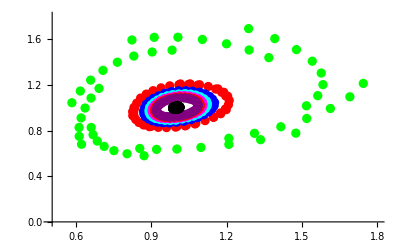

{κ,λ} for the last 50 iterations:

(1.01429 | 1.00697
0.999811 | 0.985913
0.986006 | 1.00019
1.00722 | 1.01419
1.01054 | 0.992827
0.987617 | 0.989571)

```mathematica
λκ=λκ3; (* change here *)
kmax=kmaxV[[3]]; (* change here *)
xyrange={{0.5,1.8},{0.4,1.8}}; (* change here *)
xyrange=Automatic;
Plt[1]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,50,100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,550,600}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,1050,1100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,1550,1600}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,2050,2100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,2550,2600}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,3050,3100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Purple];
Plt[8]=ListPlot[Table[{Part[λκ3,i][[1]],Part[λκ3,i][[2]]},{i,kmax-50,kmax}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Black];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:"];
Table[Part[λκ3,i],{i,kmax-5,kmax}]//MatrixForm
```

3) μ=4.0; kmax=100000

20000

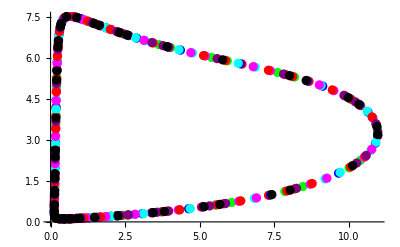

{κ,λ} for the last 50 iterations:

(3.81738 | 0.380348
0.137131 | 0.230873
0.330076 | 7.13776
10.9402 | 3.48259
0.475413 | 0.111408
0.157267 | 2.3789)

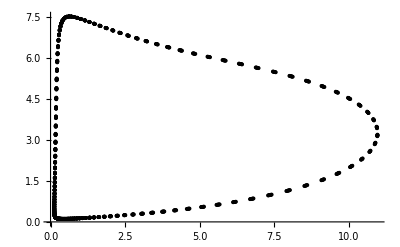

```mathematica
kmax=20000
Plt[1]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,50,100}],PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,550,600}],PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,1050,1100}],PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,1550,1600}],PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,2050,2100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,2550,2600}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,3050,3100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Purple];
Plt[8]=ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,kmax-50,kmax}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Black];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:"];
Table[Part[λκ4,i],{i,kmax-5,kmax}]//MatrixForm
ListPlot[Table[{Part[λκ4,i][[1]],Part[λκ4,i][[2]]},{i,kmax-1000,kmax}],PlotRange->Full,PlotStyle->Black]
```

```mathematica
Clear[μ,η]
kmax=20000;
InitRG;
η=N[1.0,2000];
μ=N[10.0,2000];
λκt=ConstantArray[0,{kmax,2}];
Jocnumt=ConstantArray[0,{kmax,2}];
For[i=1,i<=kmax,i+=1,
RG;
Part[λκt,i][[1]]=A[3]/.SAT;
Part[λκt,i][[2]]=A[4]/.SAT;
Jciter1=(Jc/.Sκλ2)/.SAT;
Part[Jocnum,i][[1]]=Jciter[[1]];
Part[Jocnum5,i][[2]]=Jciter[[2]];
]
```

```mathematica
Clear[μ,η]
kmax=20000;
InitRG;
η=N[1.0,2000];
μ=N[100.0,2000];
λκ5=ConstantArray[0,{kmax,2}];
Jocnum5=ConstantArray[0,{kmax,2}];
For[i=1,i<=kmax,i+=1,
RG;
Part[λκ5,i][[1]]=A[3]/.SAT;
Part[λκ5,i][[2]]=A[4]/.SAT;
Jciter1=(Jc/.Sκλ2)/.SAT;
Part[Jocnum5,i][[1]]=Jciter[[1]];
Part[Jocnum5,i][[2]]=Jciter[[2]];
]
```

20000

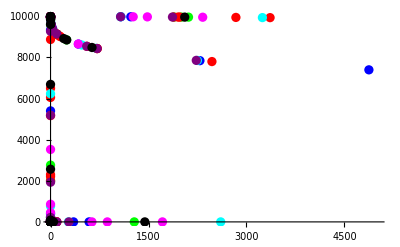

{κ,λ} for the last 50 iterations:

(44.8767 | 0.000223011
5.06704×10^-6 | 0.00104175
0.0000537923 | 9989.87
5423.29 | 9893.29
1.86088 | 0.000103721
0.0000562519 | 0.29643)

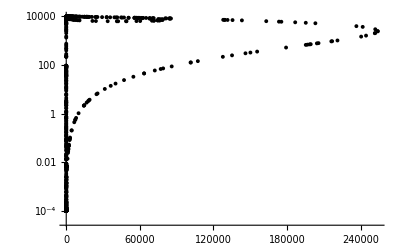

```mathematica
kmax=20000
Plt[1]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,50,100}],PlotStyle->Green];
Plt[2]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,550,600}],PlotStyle->Red];
Plt[3]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,1050,1100}],PlotStyle->Blue];
Plt[4]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,1550,1600}],PlotStyle->Cyan];
Plt[5]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,2050,2100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Magenta];
Plt[6]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,2550,2600}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Red];
Plt[7]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,3050,3100}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Purple];
Plt[8]=ListPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,kmax-50,kmax}],PlotRange->{{0.5,1.8},{0,1.8}},PlotStyle->Black];
Show[Table[Plt[i],{i,1,8}]]
Print["{κ,λ} for the last 50 iterations:"];
Table[Part[λκ5,i],{i,kmax-5,kmax}]//MatrixForm
ListLogPlot[Table[{Part[λκ5,i][[1]],Part[λκ5,i][[2]]},{i,kmax-1000,kmax}],PlotRange->Full,PlotStyle->Black]
```

Jacobian Analysis

```mathematica
ind=1; (* change here *)
Jocnum=Abs[Jocnum1]; (* change here *)
kmax=kmaxV[[ind]];
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", Table[Jocnum[[i]],{i,1,5}]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", Table[Jocnum[[i]],{i,kmax-5,kmax}]//MatrixForm]
```

μ=1.; kmax=3000; Eigenvalues of first 5 Jocabians:(0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.)

μ=1.; kmax=3000; Eigenvalues of Last 5 Jocabians:(0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.)

```mathematica
ind=2; (* change here *)
Jocnum=Abs[Jocnum2]; (* change here *)
kmax=kmaxV[[ind]];
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", Table[Jocnum[[i]],{i,1,5}]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", Table[Jocnum[[i]],{i,kmax-5,kmax}]//MatrixForm]
```

μ=2.; kmax=3000; Eigenvalues of first 5 Jocabians:(1.10579 | 1.10579
1.13673 | 1.13673
0.588408 | 0.588408
0.725018 | 0.725018
1.02907 | 1.02907)

μ=2.; kmax=3000; Eigenvalues of Last 5 Jocabians:(0.816497 | 0.816497
0.816497 | 0.816497
0.816497 | 0.816497
0.816497 | 0.816497
0.816497 | 0.816497
0.816497 | 0.816497)

```mathematica
ind=3; (* change here *)
Jocnum=Abs[Jocnum3]; (* change here *)
kmax=kmaxV[[ind]];
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", Table[Jocnum[[i]],{i,1,5}]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", Table[Jocnum[[i]],{i,kmax-5,kmax}]//MatrixForm]
```

μ=3.; kmax=100000; Eigenvalues of first 5 Jocabians:(2.22359 | 2.22359
2.29055 | 2.29055
0.259957 | 0.259957
0.873083 | 0.873083
2.71606 | 2.71606)

μ=3.; kmax=100000; Eigenvalues of Last 5 Jocabians:(0.982385 | 0.982385
1.00024 | 1.00024
1.01773 | 1.01773
0.991033 | 0.991033
0.986961 | 0.986961
1.01567 | 1.01567)

```mathematica
ind=4; (* change here *)
Jocnum=Abs[Jocnum4]; (* change here *)
kmax=kmaxV[[ind]];
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", Table[Jocnum[[i]],{i,1,5}]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", Table[Jocnum[[i]],{i,kmax-5,kmax}]//MatrixForm]
```

μ=4.; kmax=100000; Eigenvalues of first 5 Jocabians:(3.8267 | 3.8267
3.91876 | 3.91876
0.0886725 | 0.0886725
1.17059 | 1.17059
6.00511 | 6.00511)

μ=4.; kmax=100000; Eigenvalues of Last 5 Jocabians:(0.0833919 | 0.0833919
6.57117 | 6.57117
4.84635 | 4.84635
0.0345382 | 0.0242398
2.00104 | 2.00104
6.74707 | 6.74707)

```mathematica
ind=5; (* change here *)
Jocnum=Abs[Jocnum5]; (* change here *)
kmax=kmaxV[[ind]];
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", Table[Jocnum[[i]],{i,1,5}]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", Table[Jocnum[[i]],{i,kmax-5,kmax}]//MatrixForm]
```

μ=5.; kmax=100000; Eigenvalues of first 5 Jocabians:(5.93147 | 5.93147
6.04098 | 6.04098
0.069243 | 0.0151338
1.61344 | 1.61344
10.532 | 10.532)

μ=5.; kmax=100000; Eigenvalues of Last 5 Jocabians:(3.58791 | 3.58791
11.2284 | 11.2284
0.74317 | 0.014037
0.139698 | 0.139698
11.9204 | 11.9204
6.33276 | 6.33276)

```mathematica
ind=6; (* change here *)
Jocnum=Abs[Jocnum6]; (* change here *)
kmax=kmaxV[[ind]];
kmax=4600;
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", N[Table[Jocnum[[i]],{i,1,5}],6]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", N[Table[Jocnum[[i]],{i,kmax-5,kmax}],6]//MatrixForm]
```

μ=10.; kmax=4600; Eigenvalues of first 5 Jocabians:(23.9968 | 23.9968
24.1454 | 24.1454
0.00609583 | 0.000168903
5.5537 | 5.5537
10.7776 | 182.529)

μ=10.; kmax=4600; Eigenvalues of Last 5 Jocabians:(0.00733769 | 0.0000253816
1.78028 | 1.78028
23.7079 | 73.2389
23.8615 | 0.00911466
0.00164444 | 0.00164444
38.6563 | 38.6563)

```mathematica
ind=7; (* change here *)
Jocnum=Abs[Jocnum7]; (* change here *)
kmax=kmaxV[[ind]];
kmax=4600;
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", N[Table[Jocnum[[i]],{i,1,5}],6]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", N[Table[Jocnum[[i]],{i,kmax-5,kmax}],6]//MatrixForm]
```

μ=20.; kmax=4600; Eigenvalues of first 5 Jocabians:(97.7057 | 97.7057
390.933 | 24.504
0.000396776 | 2.26131×10^-6
21.2002 | 21.2002
8.18218 | 3426.8)

μ=20.; kmax=4600; Eigenvalues of Last 5 Jocabians:(0.000999943 | 0.000999943
72.059 | 72.059
0.0643687 | 150387.
0.00618839 | 1.10717×10^-6
0.557025 | 0.557025
104.866 | 104.866)

```mathematica
ind=8; (* change here *)
Jocnum=Abs[Jocnum8]; (* change here *)
kmax=kmaxV[[ind]];
kmax=4600;
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of first 5 Jocabians:", N[Table[Jocnum[[i]],{i,1,5}],6]//MatrixForm]
Print["μ=",N[μV[[ind]],4],"; kmax=",kmax,"; Eigenvalues of Last 5 Jocabians:", N[Table[Jocnum[[i]],{i,kmax-5,kmax}],6]//MatrixForm]
```

μ=100.; kmax=4600; Eigenvalues of first 5 Jocabians:(2487.67 | 2487.67
59979.7 | 103.192
6.39858×10^-7 | 1.30715×10^-10
510.952 | 510.952
7.22394 | 2.16631×10^6)

μ=100.; kmax=4600; Eigenvalues of Last 5 Jocabians:(1.96236×10^-8 | 1.96236×10^-8
2618.7 | 2618.7
0.081294 | 8.06653×10^7
8.21335×10^-6 | 6.3816×10^-11
16.87 | 16.87
55.0629 | 107413.)

```mathematica
N[Abs[-((1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√((-λ-λ μ+κ λ μ+κ λ μ^2)^2-4 (-2 κ^2-2 κ μ-2 κ^3 μ+2 κ μ^3+2 κ^3 μ^3+2 κ^2 μ^4))))/(2 (1+κ μ)^3)],5]
```

50.5 Abs[(-101. λ+10100. κ λ+√(-4. (1.9998×10^6 κ+2.×10^8 κ^2+1.9998×10^6 κ^3)+(-101. λ+10100. κ λ)^2))/(1.+100. κ)^3]